```mathematica
PDF[UniformDistribution[{0,2Pi}],x]
```

Piecewise[{{1/(2 π), 0≤x≤2 π}, {0, True}}]

```mathematica
Convolve[PDF[UniformDistribution[{0,2Pi}],x],Simplify[PDF[UniformDistribution[{0,2Pi}],-x]],x,z]//Simplify
```

Piecewise[{{-(-2 π+z)/(4 π^2), 0<z<2 π}, {(2 π+z)/(4 π^2), -2 π<z≤0}, {0, True}}]

```mathematica
PDF[TriangularDistribution[{-2Pi,2Pi}],x]
```

Piecewise[{{(2 π+x)/(4 π^2), -2 π≤x≤0}, {(2 π-x)/(4 π^2), 0<x≤2 π}, {0, True}}]

```mathematica
Convolve[PDF[TriangularDistribution[{-2Pi,2Pi}],x],Simplify[PDF[TriangularDistribution[{-2Pi,2Pi}],-x]],x,z]//Simplify
```

Piecewise[{{(32 π^3-12 π z^2-3 z^3)/(96 π^4), -2 π<z≤0}, {(4 π-z)^3/(96 π^4), 2 π≤z<4 π}, {(4 π+z)^3/(96 π^4), -4 π<z≤-2 π}, {(32 π^3-12 π z^2+3 z^3)/(96 π^4), 0<z<2 π}, {0, True}}]

```mathematica
px[x_]:=Piecewise[{{(4 π+x)^3/(96 π^4),-4Pi<x≤-2Pi},{(32 π^3-12 π x^2-3 x^3)/(96 π^4),-2 π<x≤0},{(32 π^3-12 π x^2+3 x^3)/(96 π^4),0<x<2 π},{(4 π-x)^3/(96 π^4),2 π≤x<4 π}}]
```

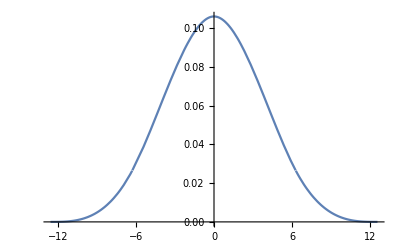

```mathematica
Plot[px[x],{x,-4Pi,4Pi}]
```

```mathematica
Convolve[PDF[TriangularDistribution[{-2Pi,2Pi}],x],Simplify[PDF[UniformDistribution[{0,2Pi}],-x]],x,z]//FullSimplify
```

Piecewise[{{-(-2 π^2+2 π z+z^2)/(8 π^3), -2 π<z≤0}, {(-2 π+z)^2/(16 π^3), 0<z<2 π}, {(4 π+z)^2/(16 π^3), -4 π<z≤-2 π}, {0, True}}]

```mathematica
py[y_]:=Piecewise[{{(4 π+y)^2/(16 π^3),-4 π<y≤-2 π},{-(-2 π^2+2 π y+y^2)/(8 π^3),-2 π<y≤0},{(-2 π+y)^2/(16 π^3),0<y<2 π}}]
```

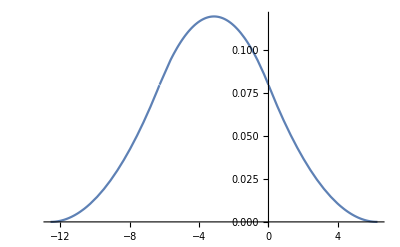

```mathematica
Plot[py[y],{y,-4Pi,2Pi}]
```

```mathematica
(4 π+y-4Pi)^2/(16 π^3)+-(-2 π^2+2 π (y-2Pi)+(y-2Pi)^2)/(8 π^3)+(-2 π+y)^2/(16 π^3)//Simplify
```

1/(2 π)

```mathematica
Integrate[Cos[x]^k,{x,0,2Pi},Assumptions->k≥0&&k∈Integers]/(2Pi)
```

((1+(-1)^k)^2 Gamma[(1+k)/2])/(2 k √π Gamma[k/2])

```mathematica
Table[((1+(-1)^k)^2 Gamma[(1+k)/2])/(4 √π Gamma[k/2+1]),{k,0,10,2}]
```

{1,1/2,3/8,5/16,35/128,63/256}

```mathematica
px[x_]:=Piecewise[{{(4 π+x)^3/(96 π^4),-4Pi<x≤-2Pi},{(32 π^3-12 π x^2-3 x^3)/(96 π^4),-2 π<x≤0},{(32 π^3-12 π x^2+3 x^3)/(96 π^4),0<x<2 π},{(4 π-x)^3/(96 π^4),2 π≤x<4 π}}]
```

```mathematica
(4 π+x-4Pi)^3/(96 π^4)+(32 π^3-12 π (x-2Pi)^2-3 (x-2Pi)^3)/(96 π^4)+(32 π^3-12 π x^2+3 x^3)/(96 π^4)+(4 π-(x+2Pi))^3/(96 π^4)//Simplify
```

1/(2 π)

## N = 2

### K=1

```mathematica
n+z^2
```

n+z^2

### K=2

```mathematica
(n+2Cos[x]+2z(Cos[y1]+Cos[y2])+z^2)^2//Expand
```

n^2+2 n z^2+z^4+4 n Cos[x]+4 z^2 Cos[x]+4 Cos[x]^2+4 n z Cos[y1]+4 z^3 Cos[y1]+8 z Cos[x] Cos[y1]+4 z^2 Cos[y1]^2+4 n z Cos[y2]+4 z^3 Cos[y2]+8 z Cos[x] Cos[y2]+8 z^2 Cos[y1] Cos[y2]+4 z^2 Cos[y2]^2

```mathematica
n^2+2 n z^2+z^4+4/2+4 z^2 /2+4 z^2 /2
```

2+n^2+4 z^2+2 n z^2+z^4

```mathematica
2+n^2+4 +2 n +2
```

8+2 n+n^2

### K=3

```mathematica
Collect[(n+2Cos[x]+2z(Cos[y1]+Cos[y2])+z^2)^3,{Cos[x],Cos[y1],Cos[y2]}]
```

n^3+3 n^2 z^2+3 n z^4+z^6+8 Cos[x]^3+8 z^3 Cos[y1]^3+(6 n^2 z+12 n z^3+6 z^5) Cos[y2]+(12 n z^2+12 z^4) Cos[y2]^2+8 z^3 Cos[y2]^3+Cos[x]^2 (12 n+12 z^2+24 z Cos[y1]+24 z Cos[y2])+Cos[y1]^2 (12 n z^2+12 z^4+24 z^3 Cos[y2])+Cos[y1] (6 n^2 z+12 n z^3+6 z^5+(24 n z^2+24 z^4) Cos[y2]+24 z^3 Cos[y2]^2)+Cos[x] (6 n^2+12 n z^2+6 z^4+24 z^2 Cos[y1]^2+(24 n z+24 z^3) Cos[y2]+24 z^2 Cos[y2]^2+Cos[y1] (24 n z+24 z^3+48 z^2 Cos[y2]))

```mathematica
n^3+3 n^2 z^2+3 n z^4+z^6+(12 n z^2+12 z^4) /2+(12 n+12 z^2)/2+(12 n z^2+12 z^4)/2//Simplify//Expand
```

6 n+n^3+6 z^2+12 n z^2+3 n^2 z^2+12 z^4+3 n z^4+z^6

```mathematica
6 n+n^3+6 +12 n +3 n^2 +12 *2+3 n *2+6
```

36+24 n+3 n^2+n^3

### K=4

```mathematica
Collect[(n+2Cos[x]+2z(Cos[y1]+Cos[y2])+z^2)^4,{Cos[x],Cos[y1],Cos[y2]}]
```

n^4+4 n^3 z^2+6 n^2 z^4+4 n z^6+z^8+16 Cos[x]^4+16 z^4 Cos[y1]^4+(8 n^3 z+24 n^2 z^3+24 n z^5+8 z^7) Cos[y2]+(24 n^2 z^2+48 n z^4+24 z^6) Cos[y2]^2+(32 n z^3+32 z^5) Cos[y2]^3+16 z^4 Cos[y2]^4+Cos[x]^3 (32 n+32 z^2+64 z Cos[y1]+64 z Cos[y2])+Cos[y1]^3 (32 n z^3+32 z^5+64 z^4 Cos[y2])+Cos[y1]^2 (24 n^2 z^2+48 n z^4+24 z^6+(96 n z^3+96 z^5) Cos[y2]+96 z^4 Cos[y2]^2)+Cos[y1] (8 n^3 z+24 n^2 z^3+24 n z^5+8 z^7+(48 n^2 z^2+96 n z^4+48 z^6) Cos[y2]+(96 n z^3+96 z^5) Cos[y2]^2+64 z^4 Cos[y2]^3)+Cos[x]^2 (24 n^2+48 n z^2+24 z^4+96 z^2 Cos[y1]^2+(96 n z+96 z^3) Cos[y2]+96 z^2 Cos[y2]^2+Cos[y1] (96 n z+96 z^3+192 z^2 Cos[y2]))+Cos[x] (8 n^3+24 n^2 z^2+24 n z^4+8 z^6+64 z^3 Cos[y1]^3+(48 n^2 z+96 n z^3+48 z^5) Cos[y2]+(96 n z^2+96 z^4) Cos[y2]^2+64 z^3 Cos[y2]^3+Cos[y1]^2 (96 n z^2+96 z^4+192 z^3 Cos[y2])+Cos[y1] (48 n^2 z+96 n z^3+48 z^5+(192 n z^2+192 z^4) Cos[y2]+192 z^3 Cos[y2]^2))

```mathematica
n^4+4 n^3 z^2+6 n^2 z^4+4 n z^6+z^8+16 *3/8+16 z^4 *3/8+(24 n^2 z^2+48 n z^4+24 z^6) /2+16 z^4 *3/8+(24 n^2 z^2+48 n z^4+24 z^6+96 z^4 /2)/2+ (24 n^2+48 n z^2+24 z^4+96 z^2 /2+96 z^2 /2)/2//Simplify//Expand
```

6+12 n^2+n^4+48 z^2+24 n z^2+24 n^2 z^2+4 n^3 z^2+48 z^4+48 n z^4+6 n^2 z^4+24 z^6+4 n z^6+z^8

```mathematica
Collect[6+12 n^2+n^4+48 z^2+24 n z^2+24 n^2 z^2+4 n^3 z^2+48 z^4+48 n z^4+6 n^2 z^4+24 z^6+4 n z^6+z^8,z^2]
```

6+12 n^2+n^4+(48+24 n+24 n^2+4 n^3) z^2+(48+48 n+6 n^2) z^4+(24+4 n) z^6+z^8

```mathematica
6+12 n^2+n^4+(48+24 n+24 n^2+4 n^3) +(48+48 n+6 n^2) 2+(24+4 n) Factorial[3]+Factorial[4]//Simplify
```

318+144 n+48 n^2+4 n^3+n^4

### K=5

```mathematica
Collect[(n+2Cos[x]+2z(Cos[y1]+Cos[y2])+z^2)^5,{Cos[x],Cos[y1],Cos[y2]}]
```

n^5+5 n^4 z^2+10 n^3 z^4+10 n^2 z^6+5 n z^8+z^10+32 Cos[x]^5+32 z^5 Cos[y1]^5+(10 n^4 z+40 n^3 z^3+60 n^2 z^5+40 n z^7+10 z^9) Cos[y2]+(40 n^3 z^2+120 n^2 z^4+120 n z^6+40 z^8) Cos[y2]^2+(80 n^2 z^3+160 n z^5+80 z^7) Cos[y2]^3+(80 n z^4+80 z^6) Cos[y2]^4+32 z^5 Cos[y2]^5+Cos[x]^4 (80 n+80 z^2+160 z Cos[y1]+160 z Cos[y2])+Cos[y1]^4 (80 n z^4+80 z^6+160 z^5 Cos[y2])+Cos[y1]^3 (80 n^2 z^3+160 n z^5+80 z^7+(320 n z^4+320 z^6) Cos[y2]+320 z^5 Cos[y2]^2)+Cos[y1]^2 (40 n^3 z^2+120 n^2 z^4+120 n z^6+40 z^8+(240 n^2 z^3+480 n z^5+240 z^7) Cos[y2]+(480 n z^4+480 z^6) Cos[y2]^2+320 z^5 Cos[y2]^3)+Cos[y1] (10 n^4 z+40 n^3 z^3+60 n^2 z^5+40 n z^7+10 z^9+(80 n^3 z^2+240 n^2 z^4+240 n z^6+80 z^8) Cos[y2]+(240 n^2 z^3+480 n z^5+240 z^7) Cos[y2]^2+(320 n z^4+320 z^6) Cos[y2]^3+160 z^5 Cos[y2]^4)+Cos[x]^3 (80 n^2+160 n z^2+80 z^4+320 z^2 Cos[y1]^2+(320 n z+320 z^3) Cos[y2]+320 z^2 Cos[y2]^2+Cos[y1] (320 n z+320 z^3+640 z^2 Cos[y2]))+Cos[x]^2 (40 n^3+120 n^2 z^2+120 n z^4+40 z^6+320 z^3 Cos[y1]^3+(240 n^2 z+480 n z^3+240 z^5) Cos[y2]+(480 n z^2+480 z^4) Cos[y2]^2+320 z^3 Cos[y2]^3+Cos[y1]^2 (480 n z^2+480 z^4+960 z^3 Cos[y2])+Cos[y1] (240 n^2 z+480 n z^3+240 z^5+(960 n z^2+960 z^4) Cos[y2]+960 z^3 Cos[y2]^2))+Cos[x] (10 n^4+40 n^3 z^2+60 n^2 z^4+40 n z^6+10 z^8+160 z^4 Cos[y1]^4+(80 n^3 z+240 n^2 z^3+240 n z^5+80 z^7) Cos[y2]+(240 n^2 z^2+480 n z^4+240 z^6) Cos[y2]^2+(320 n z^3+320 z^5) Cos[y2]^3+160 z^4 Cos[y2]^4+Cos[y1]^3 (320 n z^3+320 z^5+640 z^4 Cos[y2])+Cos[y1]^2 (240 n^2 z^2+480 n z^4+240 z^6+(960 n z^3+960 z^5) Cos[y2]+960 z^4 Cos[y2]^2)+Cos[y1] (80 n^3 z+240 n^2 z^3+240 n z^5+80 z^7+(480 n^2 z^2+960 n z^4+480 z^6) Cos[y2]+(960 n z^3+960 z^5) Cos[y2]^2+640 z^4 Cos[y2]^3))

```mathematica
n^5+5 n^4 z^2+10 n^3 z^4+10 n^2 z^6+5 n z^8+z^10+(40 n^3 z^2+120 n^2 z^4+120 n z^6+40 z^8)1/2+(80 n z^4+80 z^6) 3/8+3/8(80 n+80 z^2)+3/8(80 n z^4+80 z^6)+1/2(40 n^3 z^2+120 n^2 z^4+120 n z^6+40 z^8+(480 n z^4+480 z^6) 1/2)+1/2(40 n^3+120 n^2 z^2+120 n z^4+40 z^6+(480 n z^2+480 z^4)1/2+1/2(480 n z^2+480 z^4))//Simplify
```

n^5+5 n^4 z^2+10 n^3 (2+4 z^2+z^4)+10 n^2 z^2 (6+12 z^2+z^4)+5 n (6+48 z^2+48 z^4+24 z^6+z^8)+z^2 (30+240 z^2+200 z^4+40 z^6+z^8)

```mathematica
Collect[n^5+5 n^4 z^2+10 n^3 (2+4 z^2+z^4)+10 n^2 z^2 (6+12 z^2+z^4)+5 n (6+48 z^2+48 z^4+24 z^6+z^8)+z^2 (30+240 z^2+200 z^4+40 z^6+z^8),z^2]
```

30 n+20 n^3+n^5+(30+240 n+60 n^2+40 n^3+5 n^4) z^2+(240+240 n+120 n^2+10 n^3) z^4+(200+120 n+10 n^2) z^6+(40+5 n) z^8+z^10

```mathematica
30 n+20 n^3+n^5+(30+240 n+60 n^2+40 n^3+5 n^4) +(240+240 n+120 n^2+10 n^3) 2+(200+120 n+10 n^2) Factorial[3]+(40+5 n) Factorial[4]+Factorial[5]//Simplify
```

2790+1590 n+360 n^2+80 n^3+5 n^4+n^5

#### K=6

```mathematica
Collect[(n+2Cos[x]+2z(Cos[y1]+Cos[y2])+z^2)^6,{Cos[x],Cos[y1],Cos[y2]}]
```

n^6+6 n^5 z^2+15 n^4 z^4+20 n^3 z^6+15 n^2 z^8+6 n z^10+z^12+64 Cos[x]^6+64 z^6 Cos[y1]^6+(12 n^5 z+60 n^4 z^3+120 n^3 z^5+120 n^2 z^7+60 n z^9+12 z^11) Cos[y2]+(60 n^4 z^2+240 n^3 z^4+360 n^2 z^6+240 n z^8+60 z^10) Cos[y2]^2+(160 n^3 z^3+480 n^2 z^5+480 n z^7+160 z^9) Cos[y2]^3+(240 n^2 z^4+480 n z^6+240 z^8) Cos[y2]^4+(192 n z^5+192 z^7) Cos[y2]^5+64 z^6 Cos[y2]^6+Cos[x]^5 (192 n+192 z^2+384 z Cos[y1]+384 z Cos[y2])+Cos[y1]^5 (192 n z^5+192 z^7+384 z^6 Cos[y2])+Cos[y1]^4 (240 n^2 z^4+480 n z^6+240 z^8+(960 n z^5+960 z^7) Cos[y2]+960 z^6 Cos[y2]^2)+Cos[y1]^3 (160 n^3 z^3+480 n^2 z^5+480 n z^7+160 z^9+(960 n^2 z^4+1920 n z^6+960 z^8) Cos[y2]+(1920 n z^5+1920 z^7) Cos[y2]^2+1280 z^6 Cos[y2]^3)+Cos[y1]^2 (60 n^4 z^2+240 n^3 z^4+360 n^2 z^6+240 n z^8+60 z^10+(480 n^3 z^3+1440 n^2 z^5+1440 n z^7+480 z^9) Cos[y2]+(1440 n^2 z^4+2880 n z^6+1440 z^8) Cos[y2]^2+(1920 n z^5+1920 z^7) Cos[y2]^3+960 z^6 Cos[y2]^4)+Cos[y1] (12 n^5 z+60 n^4 z^3+120 n^3 z^5+120 n^2 z^7+60 n z^9+12 z^11+(120 n^4 z^2+480 n^3 z^4+720 n^2 z^6+480 n z^8+120 z^10) Cos[y2]+(480 n^3 z^3+1440 n^2 z^5+1440 n z^7+480 z^9) Cos[y2]^2+(960 n^2 z^4+1920 n z^6+960 z^8) Cos[y2]^3+(960 n z^5+960 z^7) Cos[y2]^4+384 z^6 Cos[y2]^5)+Cos[x]^4 (240 n^2+480 n z^2+240 z^4+960 z^2 Cos[y1]^2+(960 n z+960 z^3) Cos[y2]+960 z^2 Cos[y2]^2+Cos[y1] (960 n z+960 z^3+1920 z^2 Cos[y2]))+Cos[x]^3 (160 n^3+480 n^2 z^2+480 n z^4+160 z^6+1280 z^3 Cos[y1]^3+(960 n^2 z+1920 n z^3+960 z^5) Cos[y2]+(1920 n z^2+1920 z^4) Cos[y2]^2+1280 z^3 Cos[y2]^3+Cos[y1]^2 (1920 n z^2+1920 z^4+3840 z^3 Cos[y2])+Cos[y1] (960 n^2 z+1920 n z^3+960 z^5+(3840 n z^2+3840 z^4) Cos[y2]+3840 z^3 Cos[y2]^2))+Cos[x]^2 (60 n^4+240 n^3 z^2+360 n^2 z^4+240 n z^6+60 z^8+960 z^4 Cos[y1]^4+(480 n^3 z+1440 n^2 z^3+1440 n z^5+480 z^7) Cos[y2]+(1440 n^2 z^2+2880 n z^4+1440 z^6) Cos[y2]^2+(1920 n z^3+1920 z^5) Cos[y2]^3+960 z^4 Cos[y2]^4+Cos[y1]^3 (1920 n z^3+1920 z^5+3840 z^4 Cos[y2])+Cos[y1]^2 (1440 n^2 z^2+2880 n z^4+1440 z^6+(5760 n z^3+5760 z^5) Cos[y2]+5760 z^4 Cos[y2]^2)+Cos[y1] (480 n^3 z+1440 n^2 z^3+1440 n z^5+480 z^7+(2880 n^2 z^2+5760 n z^4+2880 z^6) Cos[y2]+(5760 n z^3+5760 z^5) Cos[y2]^2+3840 z^4 Cos[y2]^3))+Cos[x] (12 n^5+60 n^4 z^2+120 n^3 z^4+120 n^2 z^6+60 n z^8+12 z^10+384 z^5 Cos[y1]^5+(120 n^4 z+480 n^3 z^3+720 n^2 z^5+480 n z^7+120 z^9) Cos[y2]+(480 n^3 z^2+1440 n^2 z^4+1440 n z^6+480 z^8) Cos[y2]^2+(960 n^2 z^3+1920 n z^5+960 z^7) Cos[y2]^3+(960 n z^4+960 z^6) Cos[y2]^4+384 z^5 Cos[y2]^5+Cos[y1]^4 (960 n z^4+960 z^6+1920 z^5 Cos[y2])+Cos[y1]^3 (960 n^2 z^3+1920 n z^5+960 z^7+(3840 n z^4+3840 z^6) Cos[y2]+3840 z^5 Cos[y2]^2)+Cos[y1]^2 (480 n^3 z^2+1440 n^2 z^4+1440 n z^6+480 z^8+(2880 n^2 z^3+5760 n z^5+2880 z^7) Cos[y2]+(5760 n z^4+5760 z^6) Cos[y2]^2+3840 z^5 Cos[y2]^3)+Cos[y1] (120 n^4 z+480 n^3 z^3+720 n^2 z^5+480 n z^7+120 z^9+(960 n^3 z^2+2880 n^2 z^4+2880 n z^6+960 z^8) Cos[y2]+(2880 n^2 z^3+5760 n z^5+2880 z^7) Cos[y2]^2+(3840 n z^4+3840 z^6) Cos[y2]^3+1920 z^5 Cos[y2]^4))

```mathematica
n^6+6 n^5 z^2+15 n^4 z^4+20 n^3 z^6+15 n^2 z^8+6 n z^10+z^12+64 5/16+64 z^6 5/16+(60 n^4 z^2+240 n^3 z^4+360 n^2 z^6+240 n z^8+60 z^10)1/2+(240 n^2 z^4+480 n z^6+240 z^8) 3/8+64 z^6 5/16+3/8(240 n^2 z^4+480 n z^6+240 z^8+960 z^6 1/2)+1/2(60 n^4 z^2+240 n^3 z^4+360 n^2 z^6+240 n z^8+60 z^10+(1440 n^2 z^4+2880 n z^6+1440 z^8) 1/2+960 z^6 3/8)+3/8(240 n^2+480 n z^2+240 z^4+960 z^2 1/2+960 z^2 1/2)+1/2(60 n^4+240 n^3 z^2+360 n^2 z^4+240 n z^6+60 z^8+960 z^4 3/8+(1440 n^2 z^2+2880 n z^4+1440 z^6)1/2+960 z^4 3/8+1/2(1440 n^2 z^2+2880 n z^4+1440 z^6+5760 z^4 1/2))//FullSimplify
```

20+90 n^2+30 n^4+n^6+6 (60+n (30+n (120+n (20+n (10+n))))) z^2+15 (78+n (96+n (4+n) (12+n))) z^4+20 (2+n)^2 (14+n) z^6+15 (38+n (16+n)) z^8+6 (10+n) z^10+z^12

```mathematica
Collect[20+90 n^2+30 n^4+n^6+6 (60+n (30+n (120+n (20+n (10+n))))) z^2+15 (78+n (96+n (4+n) (12+n))) z^4+20 (2+n)^2 (14+n) z^6+15 (38+n (16+n)) z^8+6 (10+n) z^10+z^12,z^2]
```

20+90 n^2+30 n^4+n^6+6 (60+n (30+n (120+n (20+n (10+n))))) z^2+15 (78+n (96+n (4+n) (12+n))) z^4+20 (2+n)^2 (14+n) z^6+15 (38+n (16+n)) z^8+6 (10+n) z^10+z^12

```mathematica
20+90 n^2+30 n^4+n^6+6 (60+n (30+n (120+n (20+n (10+n)))))+15 (78+n (96+n (4+n) (12+n))) 2+20 (2+n)^2 (14+n) Factorial[3]+15 (38+n (16+n)) Factorial[4]+6 (10+n) Factorial[5]+Factorial[6]//Simplify
```

31040+16740 n+4770 n^2+720 n^3+120 n^4+6 n^5+n^6